### 1 Napredna računalniška orodja: 2. domača naloga

### 1.1 Računanje vrednosti števila π

```mathematica
(*Kličem funkcijo iz shranjene datoteke*)
Get["C:\\Users\\Andrej\\Desktop\\5. Semester\\Napredna računalnipka orodja\\Mathematica\\FunkcijaMonteCarlo.m"]
```

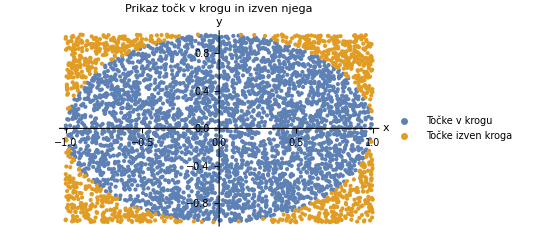

Približek izračuna števila π je 3.1232

```mathematica
i=5000;
VseTocke=MonteCarlo[i]; (*Dobimo i točk v dveh seznamih*)
Krog=VseTocke[[1]];
Kvadrat=VseTocke[[2]];
IzracunPi=N[(4 Length[Krog])/(Length[Kvadrat]+Length[Krog])];
ListPlot[{VseTocke[[1]],VseTocke[[2]]},
PlotLabel->"Prikaz točk v krogu in izven njega",
AxesLabel->{"x","y"},
PlotLegends->{"Točke v krogu","Točke izven kroga"},
PlotStyle->PointSize[Medium]]
Print["Približek izračuna števila π je ",IzracunPi]
```

### 1.2 Razvoj v vrsto in funkcija Manipulate

```mathematica
F[t_]:=Sin[t] t^2*E^-t (*Definiramo funkcijo, katere iščemo približek*)
t0=2;(*Razvoj v okolici te točke*)
n=6;(*Število členov v razvoju vrste*)
```

```mathematica
RazvojInNapaka=Series[F[t],{t,t0,n}];
FTaylor[t_]=Evaluate[Normal[RazvojInNapaka]];
```

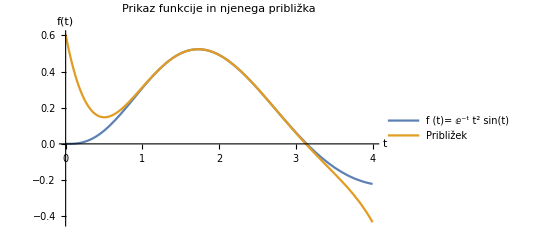

```mathematica
Plot[{F[t],FTaylor[t]},{t,0,4},
PlotLabel->"Prikaz funkcije in njenega približka",
AxesLabel->{"t","f(t)"},
PlotLegends->{"f (t)="F[t],"Približek"}]
```

```mathematica
Manipulate[Plot[{F[t],Evaluate[Normal[Series[F[t],{t,t0,a}]]]},{t,0,4},
PlotLabel->"Prikaz funkcije in njenega približka po stopnjah polinoma",
AxesLabel->{"t","f(t)"},
PlotLegends->{"f (t)="F[t],"Približek"},
PlotRange->{{0,4},{-2,1}}],
{a,1,15,1}]
```